## Using C-style RK4:

```mathematica
fx[t_,x_,v_]=v
```

v

```mathematica
k=4.9044 10^12
```

4.9044×10^12

```mathematica
x0=1781870
```

1781870

```mathematica
v0=-450
```

-450

```mathematica
fv[t_,x_,v_]=4-k/(x*x)
```

4-(4.9044×10^12)/x^2

```mathematica
RK4[h_,t0_,tf_,x0_,v0_]:=(
Lx={};
Lv={};
x=x0;
v=v0;
For[t=t0,t≤tf,t+=h,
AppendTo[Lx,{t,x}];
AppendTo[Lv,{t,v}];

k1=h fx[t,x,v];
m1=h fv[t,x,v];

k2=h fx[t+h/2, x+k1/2, v+m1/2];
m2=h fv[t+h/2, x+k1/2, v+m1/2];

k3=h fx[t+h/2, x+k2/2, v+m2/2];
m3=h fv[t+h/2, x+k2/2, v+m2/2];

k4=h fx[t+h, x+k3,v+m3];
m4=h fv[t+h,x+k3,v+m3];

x=x+(k1+2 k2 + 2 k3+k4)/6;
v=v+(m1+2 m2 + 2 m3 + m4)/6;
];
)
```

```mathematica
RK4[0.1, 0, 200, x0,v0];
```

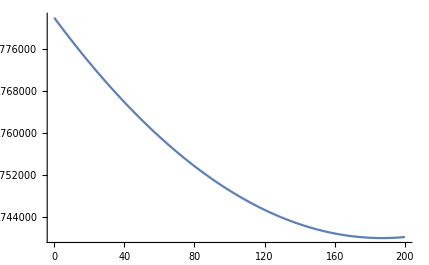

```mathematica
ListLinePlot[Lx]
```

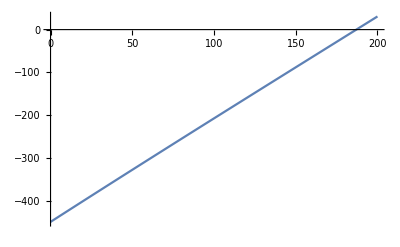

```mathematica
ListLinePlot[Lv]
```

## Using NDSolve:

```mathematica
Clear[x,v,t]

DE={x'[t]==v[t],v'[t]==4-k/(x[t]^2),x[0]==x0,v[0]==v0}
```

{x'[t]==v[t],v'[t]==4-(4.9044×10^12)/x[t]^2,x[0]==1781870,v[0]==-450}

```mathematica
sols=NDSolve[DE,{x,v},{t,0,200}]
```

{{x→InterpolatingFunction[{{0., 200.}}, <>],v→InterpolatingFunction[{{0., 200.}}, <>]}}

```mathematica
fx=Evaluate[x[t]/.sols][[1]]
```

InterpolatingFunction[{{0., 200.}}, <>][t]

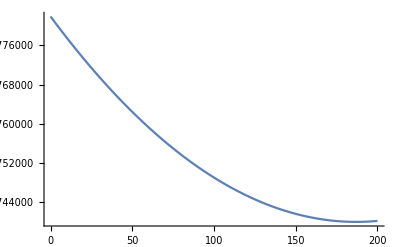

```mathematica
Plot[fx,{t,0.,200.}]
```

```mathematica
fv=Evaluate[v[t]/.sols][[1]]
```

InterpolatingFunction[{{0., 200.}}, <>][t]

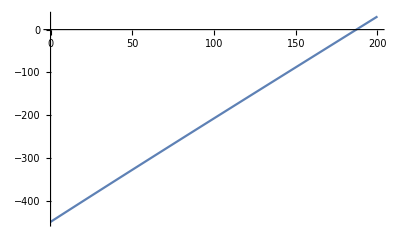

```mathematica
Plot[fv,{t,0.,200.}]
```